# Project report

## Setpoint reliability

D Malan

Department of Chemistry
University of Pretoria

17 February 2020

## Introduction

I re-wrote the gradient generator, which calculates the set points for the PID controller. This report describes the findings of the reliability study that evaluated the new gradient generator.

## Experimental

I did a simulated run with five GC runs. I compared the set points generated with the mathematical functions that described the temperature program.

## Calculations

## Results

The figure below shows how the set points are close to the mathematical function.

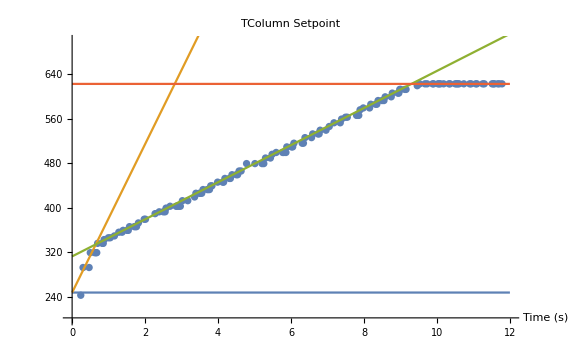

## Discussion

The computer was quite “busy” during the runs, so the data intervals are not as regular as one would like to see them, the set points hold closely to the mathematical lines. There is no systematic lag in the set points between consecutive runs.

It is slightly worrisome that there is no data point at time zero. This is not caused by the gradient generator, but by other changes to the software.

## Conclusion

The new gradient generator algorithm gives an improved  rendition of the intended temperature program.

## Recommendations

Use the new gradient generator as implemented.

Find out why there is no data point at t_r=0.